# Forecasting Fallacy

You have to make decisions that are convex.
Give a convex function. Starts with a ceiling.

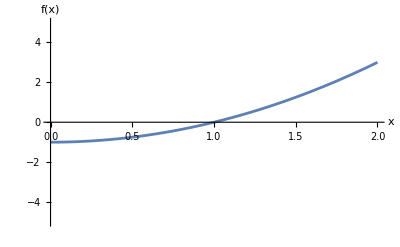

```mathematica
Plot[-1+x^2,{x,0,2},PlotRange->{-5,5},AxesLabel->{x,"f(x)"}]
```

Build a function of a vector.

```mathematica
f[X_] := Mean[1+X^2]
```

```mathematica
Subscript[X, 0]={1,1,1,1,1,1,1};
Mean[Subscript[X, 0]] //N
```

1.

```mathematica
Subscript[X, 0]={0,0,0,0,0,0,5};
Mean[Subscript[X, 0]] //N
```

0.714286

```mathematica
Subscript[X, 3]=Join[Table[0,{999}],{1000}] // Flatten;
Mean[Subscript[X, 3]] //N
```

1.

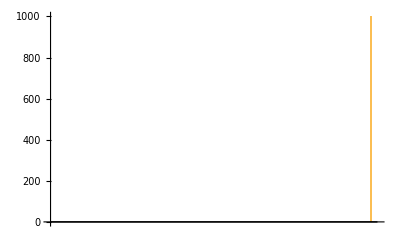

```mathematica
BarChart[Subscript[X, 3]]
```

```mathematica
f[Subscript[X, 3]]//N
```

1001.